This script is a part of ANGEL project.
V 1.0
2017.10.01
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Clearing all variables *)
```

```mathematica
m=0.047;(* Crystal mass, kg *)
a=0.02;b=0.02;l=0.04;
ρ=2600;P=10;Cp=1025;
V=a b l;m=V ρ;S=2(a b + l(b + a));
```

```mathematica
data=Import[NotebookDirectory[]<>"Kinetics.dat"][[2;;]];
```

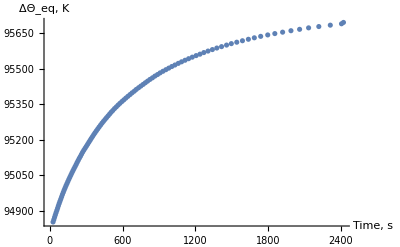

```mathematica
ListPlot[Transpose[{data[[All,1]],data[[All,2]]}],Ticks->True,AxesLabel->{"Time, s","ΔΘ_eq, K"}]
```